Preprint/Working Draft

This document is a preprint and working draft intended for community feedback.
It has not been peer-reviewed and has not been formally published.

© 2026 - Donald Airey. All rights reserved.

This work is intended for submission to a peer-reviewed journal.
Public posting of this draft does not constitute prior publication and does not waive the author’s right to publish a revised version.

# A Phenomenological Acceleration Law from Galaxy Dynamics Consistent with Type Ia Supernova Distances

## A Kinematic Origin of Gravity and Cosmic Expansion

## Abstract

We test whether a single empirically determined acceleration scale can link galaxy dynamics and cosmological distance measurements. A phenomenological acceleration law is calibrated using the baryonic Tully--Fisher relation from the SPARC galaxy sample, yielding a fixed acceleration scale. An analytic, closed-form distance--redshift relation depending on this scale is then evaluated against the Pantheon+SH0ES Type~Ia supernova dataset, with the remaining parameter calibrated on the Cepheid subset and tested on out-of-sample supernovae.

The model yields a substantially lower covariance-weighted $\chi^2$ than a spatially flat $\Lambda$CDM model with Planck 2018 parameters under identical calibration. Information criteria relative to the FLRW model give $\Delta\mathrm{AIC}=1321$ and $\Delta\mathrm{BIC}=1316$, indicating a decisive statistical preference. The distance relation is analytic and differs from the standard FLRW integral form.

These results show that a single acceleration scale inferred from galaxy dynamics can parameterize a closed-form distance--redshift relation that predicts Type~Ia supernova distances significantly more accurately than the FLRW model, without dark matter or dark energy, providing a compact and computationally efficient representation of the observed distance--redshift relation.

## Keywords

cosmology: observations -- distance scale -- supernovae: general -- galaxies: kinematics and dynamics

## Setup

### Environment Cleanup

```mathematica
Quiet@ClearAll["Global`*"];
```

### Typesetting Rules

```mathematica
MakeBoxes[accelerationSI,StandardForm]:=InterpretationBox[StyleBox["𝒜",FontFamily->"Times"],accelerationSI];
MakeBoxes[angularScale, StandardForm] := InterpretationBox[SubscriptBox["θ", "*"],angularScale]; 
MakeBoxes[baryonDensity,StandardForm]:=InterpretationBox[SubscriptBox["ρ","b"],baryonDensity];
MakeBoxes[boltzmannConstant,StandardForm]:=InterpretationBox[SubscriptBox["k",StyleBox["B",FontSlant->"Plain"]],boltzmannConstant];MakeBoxes[causalityHorizon,StandardForm]:=InterpretationBox[SubscriptBox["d","ch"],causalityHorizon];
MakeBoxes[centrifugalAcceleration,StandardForm]:=InterpretationBox[SubscriptBox["a","cent"],centrifugalAcceleration];
MakeBoxes[cephidDistanceModuli,StandardForm]:=InterpretationBox[SubscriptBox["μ","cep"],cephidDistanceModuli];
MakeBoxes[cephidRedshifts,StandardForm]:=InterpretationBox[SubscriptBox["z","cep"],cephidRedshifts];
MakeBoxes[chiSquared,StandardForm]:=InterpretationBox[SuperscriptBox["χ","2"],chiSquared];
MakeBoxes[covarianceMatrix,StandardForm]:=InterpretationBox[StyleBox["Σ",Bold],covarianceMatrix];
MakeBoxes[curvatureDensity,StandardForm]:=InterpretationBox[SubscriptBox["Ω","k"],curvatureDensity];
MakeBoxes[electronDensity,StandardForm]:=InterpretationBox[SubscriptBox["n","e"],electronDensity];
MakeBoxes[emissionTime,StandardForm]:=InterpretationBox[SubscriptBox["t","e"],emissionTime];
MakeBoxes[flrwComovingDistance,StandardForm]:=InterpretationBox[SubscriptBox["D","C,FLRW"],flrwComovingDistance];
MakeBoxes[flrwDistanceModuli,StandardForm]:=InterpretationBox[SubscriptBox["μ","FLRW"],flrwDistanceModuli];
MakeBoxes[flrwLuminousDistance,StandardForm]:=InterpretationBox[SubscriptBox["D","L,FLRW"],flrwLuminousDistance];
MakeBoxes[freeElectronFraction,StandardForm]:=InterpretationBox[SubscriptBox["X","e"],freeElectronFraction];
MakeBoxes[gasMass,StandardForm]:=InterpretationBox[SubscriptBox["M","g"],gasMass];
MakeBoxes[gasMassError,StandardForm]:=InterpretationBox[SubscriptBox["σ",SubscriptBox["M","g"]],gasMassError];
MakeBoxes[hubbleConstant,StandardForm]:=InterpretationBox[SubscriptBox["H","0"],hubbleConstant];
MakeBoxes[hydrogenMass,StandardForm]:=InterpretationBox[SubscriptBox["M","h"],hydrogenMass];
MakeBoxes[initialVelocity,StandardForm]:=InterpretationBox[SubscriptBox["V","0"],initialVelocity];
MakeBoxes[initialVelocitySI,StandardForm]:=InterpretationBox[SubscriptBox[StyleBox["𝒱",FontFamily->"Times"],"0"],initialVelocitySI];
MakeBoxes[inwardAcceleration,StandardForm]:=InterpretationBox[SubscriptBox["a","in"],inwardAcceleration];
MakeBoxes[lambdaDensity,StandardForm]:=InterpretationBox[SubscriptBox["Ω","λ"],lambdaDensity];
MakeBoxes[localSignalSpeed,StandardForm]:=InterpretationBox[SubscriptBox["c","loc"],localSignalSpeed];MakeBoxes[logTime,StandardForm]:=InterpretationBox[SubscriptBox["t","log"],logTime];
MakeBoxes[massDensity,StandardForm]:=InterpretationBox[SubscriptBox["Ω","m"],massDensity];
MakeBoxes[maximumMass,StandardForm]:=InterpretationBox[SubscriptBox["M","max"],maximumMass];
MakeBoxes[maximumRadius,StandardForm]:=InterpretationBox[SubscriptBox["r","max"],maximumRadius];
MakeBoxes[meanPhotonEnergy,StandardForm]:=InterpretationBox[RowBox[{"⟨",SubscriptBox["E","γ"],"⟩"}],meanPhotonEnergy];MakeBoxes[modelMassLog,StandardForm]:=InterpretationBox[SubscriptBox[OverscriptBox["M","^"],"log"],modelMassLog];
MakeBoxes[observationTime,StandardForm]:=InterpretationBox[SubscriptBox["t","o"],observationTime];
MakeBoxes[observationTimeSI,StandardForm]:=InterpretationBox[SubscriptBox[StyleBox["𝓉",FontFamily->"Times"],"o"],observationTimeSI];
MakeBoxes[observedMass,StandardForm]:=InterpretationBox[SubscriptBox["M","obs"],observedMass];
MakeBoxes[observedMassError,StandardForm]:=InterpretationBox[SubscriptBox["σ","M"],observedMassError];
MakeBoxes[observedMassLog,StandardForm]:=InterpretationBox[SubscriptBox["M","log"],observedMassLog];
MakeBoxes[observedMassLogError,StandardForm]:=InterpretationBox[SubscriptBox["σ","M,log"],observedMassLogError];
MakeBoxes[observedVelocity,StandardForm]:=InterpretationBox[SubscriptBox["v","obs"],observedVelocity];
MakeBoxes[observedVelocityError,StandardForm]:=InterpretationBox[SubscriptBox["σ","v"],observedVelocityError];
MakeBoxes[observedVelocityLogError,StandardForm]:=InterpretationBox[SubscriptBox["σ","v,log"],observedVelocityLogError];
MakeBoxes[particleHorizon,StandardForm]:=InterpretationBox[SubscriptBox["d","p"],particleHorizon];
MakeBoxes[photonDensity,StandardForm]:=InterpretationBox[SubscriptBox["ρ","γ"],photonDensity];
MakeBoxes[photonNumberDensity,StandardForm]:=InterpretationBox[SubscriptBox["n","γ"],photonNumberDensity];
MakeBoxes[photonTemperature,StandardForm]:=InterpretationBox[SubscriptBox["T","γ"],photonTemperature];MakeBoxes[pmeComovingDistance,StandardForm]:=InterpretationBox[SubscriptBox["D","C"],pmeComovingDistance];
MakeBoxes[pmeLuminousDistance,StandardForm]:=InterpretationBox[SubscriptBox["D","L"],pmeLuminousDistance];
MakeBoxes[pmePrediction,StandardForm]:=InterpretationBox[SubscriptBox["μ","pme"],pmePrediction];
MakeBoxes[redshiftFromTime,StandardForm]:=InterpretationBox[SubscriptBox["z","t"],redshiftFromTime];
MakeBoxes[redshiftIterator,StandardForm]:=InterpretationBox[SuperscriptBox["z","′"],redshiftIterator];
MakeBoxes[redshiftOfRecombination,StandardForm]:=InterpretationBox[SubscriptBox["z","*"],redshiftOfRecombination];
MakeBoxes[reducedPlanckConstant,StandardForm]:=InterpretationBox[StyleBox["ℏ",FontSlant->"Italic"],reducedPlanckConstant];MakeBoxes[residuals,StandardForm]:=InterpretationBox[OverscriptBox["r","→"],residuals];
MakeBoxes[scaleFactorFromTime,StandardForm]:=InterpretationBox[SubscriptBox["a","t"],scaleFactorFromTime];
MakeBoxes[soundHorizon,StandardForm]:=InterpretationBox[SubscriptBox["s","*"],soundHorizon];
MakeBoxes[speedOfCausality,StandardForm]:=InterpretationBox[SubscriptBox["c","c"],speedOfCausality];
MakeBoxes[speedOfSound,StandardForm]:=InterpretationBox[SubscriptBox["c","s"],speedOfSound];
MakeBoxes[stellarMass,StandardForm]:=InterpretationBox[SubscriptBox["M","⋆"],stellarMass];
MakeBoxes[stellarMassError,StandardForm]:=InterpretationBox[SubscriptBox["σ",SubscriptBox["M","*"]],stellarMassError];
MakeBoxes[supernovaDistanceModuli,StandardForm]:=InterpretationBox[SubscriptBox["μ","sne"],supernovaDistanceModuli];
MakeBoxes[supernovaRedshifts,StandardForm]:=InterpretationBox[SubscriptBox["z","sne"],supernovaRedshifts];
MakeBoxes[thomsonOpticalDepth,StandardForm]:=InterpretationBox[SubscriptBox["τ","T"],thomsonOpticalDepth];
MakeBoxes[thomsonScatteringCrossSection,StandardForm]:=InterpretationBox[SubscriptBox["σ","T"],thomsonScatteringCrossSection];
MakeBoxes[thomsonScatteringRate,StandardForm]:=InterpretationBox[SubscriptBox["Γ","T"],thomsonScatteringRate];
MakeBoxes[timeFromRedshift,StandardForm]:=InterpretationBox[SubscriptBox["t","z"],timeFromRedshift];
MakeBoxes[timeIterator,StandardForm]:=InterpretationBox[SuperscriptBox["t","′"],timeIterator];
MakeBoxes[timeOfRecombination,StandardForm]:=InterpretationBox[SubscriptBox["t","*"],timeOfRecombination];
MakeBoxes[transverseCircumference, StandardForm] := InterpretationBox[SubscriptBox["C", "⊥"],transverseCircumference]; 
MakeBoxes[transverseRadius, StandardForm] := InterpretationBox[SubscriptBox["R", "⊥"],transverseRadius]; 
MakeBoxes[Δs0,StandardForm]:=InterpretationBox[SuperscriptBox["Δs","0"],Δs0];
MakeBoxes[Δs1,StandardForm]:=InterpretationBox[SuperscriptBox["Δs","1"],Δs1];
MakeBoxes[Δs2,StandardForm]:=InterpretationBox[SuperscriptBox["Δs","2"],Δs2];
MakeBoxes[Δxe1,StandardForm]:=InterpretationBox[SubsuperscriptBox["Δx","e","1"],Δxe1];
MakeBoxes[Δxo1,StandardForm]:=InterpretationBox[SubsuperscriptBox["Δx","o","1"],Δxo1];
```

## Introduction

Type~Ia supernovae (SNe~Ia) provide one of the most direct observational probes of the cosmic expansion history through the luminosity distance--redshift relation. Large compilations such as Pantheon+~\cite{Brout2022}, building on earlier compilations~\cite{Scolnic2018}, and constructed using standard light-curve fitting techniques such as SALT2~\cite{Guy2007}, enable high-precision tests of cosmological models using covariance-weighted statistical methods. In the standard framework, Type~Ia supernova observations are interpreted within a parameterized expansion history specified by the Hubble constant and the relative contributions of matter, radiation, and dark energy, with spatial flatness often assumed. These parameters determine the redshift dependence of the expansion rate  and, through it, the luminosity distance.

An alternative approach is to consider constrained analytic forms for the distance--redshift relation and to evaluate their performance directly against the data. In this work, we examine a model in which the distance relation is parameterized by a small set of quantities, one of which is an acceleration scale determined independently from galaxy dynamics. This approach enables a direct test of whether a single empirically determined scale can consistently describe both galactic and cosmological observables.

The acceleration scale is obtained from fits to the baryonic Tully--Fisher relation using the SPARC galaxy sample, yielding a fixed value that is not adjusted in the supernova analysis. The remaining parameter is calibrated using the Cepheid subset of the Pantheon+ sample, and the resulting model is evaluated on the out-of-sample supernovae using the full covariance matrix.

The goal of this paper is to assess whether this constrained analytic relation provides a quantitatively consistent description of the observed SNe~Ia distance moduli across redshift under identical calibration conditions. No assumption is made regarding the underlying gravitational or cosmological theory, and the analysis is restricted to the observables considered here.

## Phenomenological Acceleration Law

The purpose of this work is to test whether a single empirically determined acceleration scale can link two otherwise distinct observational regimes: circular motion in rotationally supported galaxies and the luminosity distances of Type~Ia supernovae. We define a phenomenological acceleration law for circular orbits, determine the acceleration scale $A$ from the baryonic Tully--Fisher relation, and then hold it fixed in the supernova analysis. No underlying gravitational theory is assumed. This separation is essential: the acceleration scale entering the distance--redshift relation is not fitted to the supernova sample.

### Circular Orbits

We consider circular motion in an acceleration field consisting of a Newtonian component and a constant inward term . For a test body in a circular orbit of radius  about an enclosed baryonic mass , the radial acceleration is

```mathematica
Subscript[a, in][r_]=-A-(G M[r])/r^2
```

-A-(G M[r])/r^2

The radial acceleration of a circular orbit is:

```mathematica
Subscript[a, cent][r_]=-v^2/r;
```

The condition for circular motion then requires that this radial acceleration provide the centripetal acceleration,

```mathematica
Subscript[a, cent][r]==Subscript[a, in][r]//Simplify
```

A r+(G M[r])/r==v^2

Solving for the enclosed baryonic mass yields

```mathematica
M[v_,r_]=M[r]/.First[Solve[Subscript[a, cent][r]==Subscript[a, in][r],M[r]]]
```

-(r (A r-v^2))/G

### Circular - Orbit Solutions

This equation defines a two-parameter family of circular-orbit solutions relating baryonic mass , orbital radius , and orbital speed .

For fixed orbital speed , the mass function  is a concave quadratic in . Differentiating gives

.

The mass at a given velocity therefore reaches a maximum at

```mathematica
Subscript[r, max][v_]=r/.First[Solve[D[M[v,r], r]==0,r]]
```

v^2/(2 A)

Substituting this radius into equation (1) yields the maximum baryonic mass compatible with a circular orbit at speed ,

```mathematica
Subscript[M, max][v_]=M[v,Subscript[r, max][v]]
```

v^4/(4 A G)

The surface  defines a family of circular-orbit solutions, as shown in Figure 1, with the ridge  giving the upper envelope of baryonic mass for a given orbital speed. Galaxies dominated by circular rotation are expected to saturate this boundary and follow a characteristic mass--velocity relation.

```mathematica
Subscript[M, max][v_]=M[v,Subscript[r, max][v]]
```

v^4/(4 A G)

```mathematica
params={G->UnitConvert[Quantity["GravitationalConstant"],("Meters")^3/("Kilograms" ("Seconds")^2)],A->Quantity[1/10^11,("Meters")/("Seconds")^2]};
massSurface[v_,r_]:=ConditionalExpression[UnitConvert[M[v,r],"SolarMass"],QuantityMagnitude[UnitConvert[v^2-A r,("Meters")^2/("Seconds")^2]]>0]/.params;
massScale=1/Quantity[10^9,"SolarMass"];
fundamentalPlane=Plot3D[UnitConvert[massSurface[Quantity[v,("Kilometers")/("Seconds")],Quantity[r,"Kiloparsecs"]],"SolarMass"] massScale,{v,0,100},{r,0,30},AxesLabel->{"speed (km s^-1)","radius (kpc)","mass (10^9 M_☉)"},PlotRange->All,PlotStyle->Directive[GrayLevel[0.5]],MeshStyle->Directive[GrayLevel[0.3]],Lighting->"Neutral"];
maximumMassCurve=ParametricPlot3D[{v,QuantityMagnitude[UnitConvert[Subscript[r, max][Quantity[v,("Kilometers")/("Seconds")]],"Kiloparsecs"]],UnitConvert[Subscript[M, max][Quantity[v,("Kilometers")/("Seconds")]],"SolarMass"] massScale}/.params,{v,0,100},PlotStyle->{Directive[Red,Thick]},PlotPoints->100,MaxRecursion->4];
fundamentalPlaneFigure=Show[{fundamentalPlane,maximumMassCurve},ViewPoint->{-2,-3,1},ViewVertical->{0,0,1},ImageSize->Large]
```

-Graphics3D-

Figure 1. The baryonic mass surface  is shown as a function of orbital speed  and orbital radius  for an illustrative acceleration scale . The red ridge marks the locus  corresponding to the maximum baryonic mass permitted at each orbital speed. Galaxies populating this ridge reproduce the baryonic Tully--Fisher relation.

### Baryonic Tully--Fisher Relation

defines the scaling , consistent with the observed baryonic Tully--Fisher relation. The normalization of this relation is set by the acceleration scale . A characteristic acceleration scale in galaxy dynamics has previously been emphasized in frameworks such as MOND.

This parameter is determined empirically by fitting the circular-orbit envelope to the SPARC galaxy sample of McGaugh, Lelli and Schombert, using the assumptions , , zero intrinsic mass-to-light uncertainty, and the quality cut . These rotationally supported disk systems are well suited to this analysis, as their kinematics closely follow circular-orbit behavior.

For each galaxy the rotation curve provides an asymptotic circular velocity , while the baryonic mass  is computed as . The value of  is determined by minimizing the  statistic between the theoretical envelope and the observed  pairs.

```mathematica
tapURL="https://tapvizier.cds.unistra.fr/TAPVizieR/tap/sync";
adql="SELECT * FROM \"J/AJ/152/157/table1\"";
raw=Import[URLBuild[tapURL,<|"request"->"doQuery","lang"->"adql","format"->"csv","query"->adql|>],"CSV"];
header=First[raw];
rows=Rest[raw];
upsStar=0.5;
fracUpsErr=0.0;
gasFactor=1.33;
maxQual=3;
column=AssociationThread[header->Range[Length[header]]];
get[row_,key_]:=row[[column[key]]];
baryonicMass[row_]:=Module[{l36=N@get[row,"L3_6"],mhi=N@get[row,"MHI"]},upsStar*l36+gasFactor*mhi];
massError[row_]:=Module[{l36=N@get[row,"L3_6"],el36=N@get[row,"e_L3_6"],mhi=N@get[row,"MHI"],dist=N@get[row,"Dist"],edist=N@get[row,"e_Dist"],fracDist,eStarPhot,eStarML,eGasDist,eStarDist},fracDist=If[dist>0,edist/dist,0.0];
eStarPhot=upsStar*el36;
eStarML=fracUpsErr*upsStar*l36;
eStarDist=2*fracDist*(upsStar*l36);
eGasDist=2*fracDist*(gasFactor*mhi);
Sqrt[eStarPhot^2+eStarML^2+eStarDist^2+eGasDist^2]];
vflat[row_]:=N@get[row,"Vflat"];
vflatError[row_]:=N@get[row,"e_Vflat"];
validRowQ[row_]:=Module[{v=vflat[row],ev=vflatError[row],q=get[row,"Qual"]},NumericQ[v]&&NumericQ[ev]&&v>0&&ev>=0&&q<=maxQual];
goodRows=Select[rows,validRowQ];
btfrData=({baryonicMass[#],vflat[#],massError[#],vflatError[#]}&)/@goodRows;
```

```mathematica
G=UnitConvert[Quantity["GravitationalConstant"],("Meters")^3/("Kilograms" ("Seconds")^2)];
Msun=UnitConvert[Entity["Star","Sun"]["Mass"],"Kilograms"];
km=Quantity[1,"Kilometers"];
massScale=10.^9*Msun;
logBtfrData=Module[{mb,v,emb,ev},({mb,v,emb,ev}=#;
{Log10[mb],Log10[v],emb/(mb*Log[10]),ev/(v*Log[10])})&/@btfrData];
modelMass[Ak_?QuantityQ,v_?NumericQ]:=Module[{m},m=(Quantity[v,"Kilometers"/"Seconds"]^4)/(4 Ak G);
QuantityMagnitude[UnitConvert[m/(10.^9 Msun),1]]];
logModelMass[Ak_?QuantityQ,logv_?NumericQ]:=Log10[modelMass[Ak,10.^logv]];
chiSquareLog[Ak_?QuantityQ]:=Total[Module[{logmb,logv,slogmb,slogv,model,sigmaEff2},{logmb,logv,slogmb,slogv}=#;
model=logModelMass[Ak,logv];
sigmaEff2=slogmb^2+(4*slogv)^2;
(logmb-model)^2/sigmaEff2]&/@logBtfrData];
chiSquareLogFromLogA[aLog_?NumericQ]:=Module[{Ak},Ak=Quantity[10.^aLog,"Meters"/"Seconds"^2];
chiSquareLog[Ak]];
minimum=FindMinimum[chiSquareLogFromLogA[aLog],{aLog,Log10[3.*10^-11]},WorkingPrecision->30];
```

The best-fit acceleration scale is

```mathematica
𝒜=Quantity[10.^(aLog/. minimum[[2]]),"Meters"/"Seconds"^2]
```

3.68788×10^-11 m/s^2

The observed galaxies follow the predicted  scaling, as shown in Figure 2. The baryonic Tully--Fisher relation follows from the constant acceleration scale.

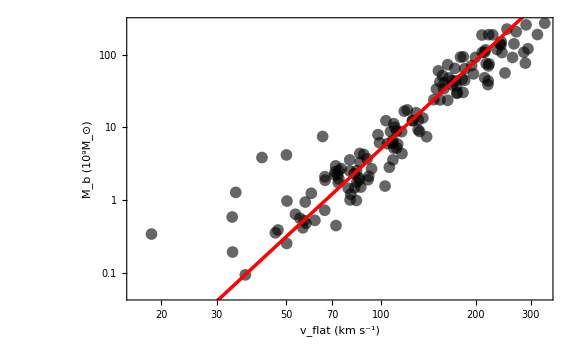

```mathematica
vMin=Min[btfrData⟦All,2⟧];
vMax=Max[btfrData⟦All,2⟧];
modelMass[v_]:=v^4/((4 A G) massScale)
observedPlot=ListLogLogPlot[btfrData⟦All,{2,1}⟧,Frame->True,Axes->False,FrameLabel->{Style[Row[{Subscript["v", "flat"]," (km s^-1)"}],14],Style[Row[{Subscript["M", "b"]," (",("10")^("9"),Subscript["M", "⊙"],")"}],14]},PlotStyle->{Directive[Black,Opacity[0.6]]},GridLines->Automatic,PlotMarkers->{Automatic,12},PlotRange->All];
modelPlot=LogLogPlot[modelMass[Quantity[v,("Kilometers")/("Seconds")]]/.A->𝒜,{v,vMin,vMax},PlotStyle->{Red,AbsoluteThickness[2.5]}];
btfrPlot=Show[observedPlot,modelPlot,ImageSize->Large]
```

Figure 2. Log--log plot of baryonic mass  versus outer rotation speed  for the SPARC galaxy sample. Black circles show the observed galaxies. The solid red line shows the circular-orbit envelope evaluated at the best-fit acceleration, demonstrating consistency with the observed  scaling.

### Distance-Redshift Relation

We consider a phenomenological analytic form for the comoving distance,

```mathematica
Subscript[D, C][z_]=(Subscript[t, o] (2 Subscript[V, 0]-A Subscript[t, o]) z)/(2+z)
```

(t_o (2 V_0-A t_o) z)/(2+z)

The luminosity distance follows as

```mathematica
Subscript[D, L][z_]=(1+z) Subscript[D, C][z]
```

(t_o (2 V_0-A t_o) z (1+z))/(2+z)

This analytic form differs from the standard FLRW integral representation and provides an alternative distance-redshift relation for comparison with observations.

### Distance Modulus

Type-Ia supernova observations are reported in terms of the distance modulus, which relates the observed luminosity distance to the measured brightness of each supernova,

```mathematica
Subscript[μ, pme][z_?NumberQ]=5 Log10[(Subscript[D, L][z])/(10 pc)];
```

### Kinematic Parameters

We treat the parameters in the analytic distance--redshift relation as kinematic quantities that set the temporal, velocity, and acceleration scales of the model, without assuming an underlying dynamical theory.

A boundary condition is imposed at the observation epoch by requiring that the parameter combination reproduce the locally measured speed of light,

This condition fixes the integration constant  in the analytic distance relation without attributing to it a direct physical interpretation as a signal velocity. Rearranging,

```mathematica
velocity=c+A Subscript[t, o];
```

With the acceleration scale  determined from the baryonic Tully--Fisher analysis, the Cepheid-calibrated Pantheon+ subset is used to determine the temporal scale , while velocity scale  is fixed algebraically by the equation above. The calibration therefore involves a single free parameter, .

For each candidate value of , theoretical distance moduli  are evaluated at the calibration-set redshifts and compared with the observed values , defining the residual vector

.

The temporal scale  is then determined by minimizing the covariance-weighted  statistic

where  is the full Pantheon+ STAT+SYS covariance matrix. The resulting best-fit value of  determines , completing the kinematic parameter set. The resulting parameters are listed in Table 1.

```mathematica
pantheonDirectory="https://github.com/PantheonPlusSH0ES/DataRelease/raw/refs/heads/main/Pantheon+_Data/4_DISTANCES_AND_COVAR/";
dataUrl=StringJoin[pantheonDirectory,"Pantheon+SH0ES.dat"];
covarianceUrl=StringJoin[pantheonDirectory,"Pantheon+SH0ES_STAT+SYS.cov"];
pantheonData=Import[dataUrl,"Table",HeaderLines->1];
covarianceData=Import[covarianceUrl,"Table"];
rawCovariance=Flatten[covarianceData];
dimensionSize=rawCovariance[[1]];
covarianceMatrix=ArrayReshape[Rest[rawCovariance],{dimensionSize,dimensionSize}];
cephidMask=pantheonData[[All,14]];
cephidIndices=Flatten@Position[cephidMask,1];
supernovaIndices=Flatten@Position[cephidMask,0];
cephidData=pantheonData[[cephidIndices]];
cephidRedshifts=N@cephidData[[All,3]];
cephidDistanceModuli=N@cephidData[[All,13]];
cephidCovarianceMatrix=covarianceMatrix[[cephidIndices,cephidIndices]];
cephidCovarianceMatrix=N[(cephidCovarianceMatrix+Transpose[cephidCovarianceMatrix])/2];
supernovaData=pantheonData[[supernovaIndices]];
supernovaRedshifts=N@supernovaData[[All,3]];
supernovaDistanceModuli=N@supernovaData[[All,11]];
supernovaCovarianceMatrix=covarianceMatrix[[supernovaIndices,supernovaIndices]];
supernovaCovarianceMatrix=N[(supernovaCovarianceMatrix+Transpose[supernovaCovarianceMatrix])/2];
```

```mathematica
params={pc->QuantityMagnitude[UnitConvert[Quantity[1,"Parsecs"],"Meters"]],c->QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"],("Meters")/("Seconds")]],A->QuantityMagnitude[𝒜]};
χ^2[t_?NumericQ]:=Module[{r^(->)},r^(->)=Subscript[μ, cep]-Subscript[μ, pme]/@Subscript[z, cep]/.params/.{Subscript[t, o]->t,Subscript[V, 0]->(velocity/.params/.{Subscript[t, o]->t})};r^(->).LinearSolve[cephidCovarianceMatrix,r^(->)]]
result=FindMinimum[χ^2[Exp[Subscript[t, log]]],{Subscript[t, log],Log[10^17]},Method->"QuasiNewton",AccuracyGoal->6];
```

```mathematica
Subscript[𝓉, o]=Quantity[Exp[Subscript[t, log]/.result⟦2⟧],"Seconds"];
Subscript[𝒱, 0]=Quantity[velocity/.params/.{Subscript[t, o]->Exp[Subscript[t, log]/.result⟦2⟧]},("Meters")/("Seconds")];
kinematicParameters={A->𝒜,Subscript[V, 0]->Subscript[𝒱, 0],Subscript[t, o]->Subscript[𝓉, o]};
Grid[{{"A",ScientificForm[A,4]},{"V_0",ScientificForm[Subscript[V, 0],4]},{"t_o",ScientificForm[Subscript[t, o],4]}}/.kinematicParameters,Frame->All,ItemStyle->12]
```

A | 3.688×10^-11 m/s^2
V_0 | 3.164×10^8 m/s
t_o | 4.512×10^17 s

Table 1 - Kinematic parameters determined from BTFR and Cepheid-calibrated Pantheon+ subset.

```mathematica
aLogBest=aLog/. minimum[[2]];
h=1*^-4;
d2=(chiSquareLogFromLogA[aLogBest+h]-2*chiSquareLogFromLogA[aLogBest]+chiSquareLogFromLogA[aLogBest-h])/h^2;
sigmaLogA=1/Sqrt[d2];
aLow=Quantity[10.^(aLogBest-sigmaLogA),"Meters"/"Seconds"^2];
aHigh=Quantity[10.^(aLogBest+sigmaLogA),"Meters"/"Seconds"^2];
deltaA=accelerationSI*sigmaLogA*Log[10]
```

5.94941×10^-13 m/s^2

### Type Ia Supernovae

We compare the analytic distance--redshift relation with the Pantheon+SH0ES Type~Ia supernova dataset using covariance-weighted statistics. The resulting Hubble diagram and residuals are shown in Figure 3.

The Pantheon+SH0ES dataset provides observed distance moduli  calibrated on an absolute scale via the SH0ES determination of the Type Ia supernova absolute magnitude. This calibration is applied to both models.

Each model predicts , which is mapped to  using the definition of the distance modulus. We compare  to  using the full Pantheon+ STAT+SYS covariance matrix.

```mathematica
pmeParams={A->𝒜,Subscript[V, 0]->Subscript[𝒱, 0],Subscript[t, o]->Subscript[𝓉, o],pc->UnitConvert[Quantity[1,"Parsecs"],"Meters"]};
flrwParams={Subscript[Ω, m]->0.315,Subscript[Ω, k]->0};
flrwParams=Join[flrwParams,{Subscript[Ω, λ]->(1-Subscript[Ω, m]-Subscript[Ω, k])/.flrwParams,Subscript[H, 0]->UnitConvert[Quantity[67.4,("Kilometers")/("Seconds" "Megaparsecs")]/. flrwParams,1/"Seconds"],pc->UnitConvert[Quantity[1,"Parsecs"],"Meters"],c->UnitConvert[Quantity["SpeedOfLight"],("Meters")/("Seconds")]}];
```

```mathematica
supernovaObservedPoints = Transpose[{supernovaRedshifts, supernovaDistanceModuli}]; 
pmePredictedPoints = Transpose[{supernovaRedshifts, pmePrediction /@ supernovaRedshifts /. pmeParams}]; 
observedPlot = ListPlot[supernovaObservedPoints, PlotStyle -> {Gray}, PlotMarkers -> {"●", Medium}, PlotRange -> All]; 
pmeLine = ListLinePlot[pmePredictedPoints, PlotStyle -> {Red, Thick}, PlotRange -> All]; 
hubbleFunction[z_] := Sqrt[massDensity*(1 + z)^3 + curvatureDensity*(1 + z)^2 + lambdaDensity];
hubbleFunctionSI[(z_)?NumericQ] := Evaluate[hubbleFunction[z] /. flrwParams];
flrwComovingDistance[z_] := (c/hubbleConstant)*NIntegrate[1/hubbleFunctionSI[redshiftIterator], {redshiftIterator, 0, z}]; 
flrwLuminousDistance[z_] := (1 + z)*flrwComovingDistance[z]; 
flrwDistanceModuli[(z_)?NumericQ] := 5*Log10[flrwLuminousDistance[z]/(10*pc)]; 
xMin = Min[supernovaRedshifts]; 
xMax = Max[supernovaRedshifts]; 
xRange = {xMin, xMax}; 
commonOptions = Sequence[ImageSize -> 700, PlotRangePadding -> Scaled[0.02], Frame -> True, FrameTicksStyle -> 12];
```

```mathematica
flrwPoints = Transpose[{supernovaRedshifts, flrwDistanceModuli /@ supernovaRedshifts /. flrwParams}]; 
flrwLine = ListLinePlot[flrwPoints, PlotStyle -> {RGBColor[0, 0, 1], Thick}, PlotRange -> All]; 
hubblePlot = Show[{observedPlot, pmeLine, flrwLine}, commonOptions, PlotRange -> {xRange, All}, FrameLabel -> {None, Style["Distance Modulus (μ)", 14]}, 
    FrameTicks -> {{Automatic, Automatic}, {None, None}}, ImagePadding -> {{70, 20}, {0, 20}}];
```

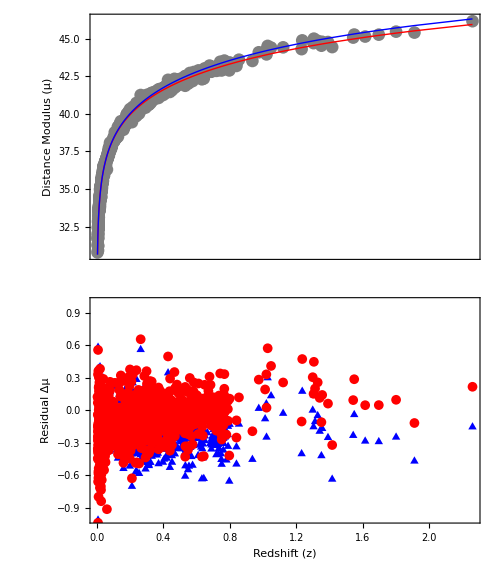

```mathematica
pmeResiduals = supernovaDistanceModuli - (pmePrediction /@ supernovaRedshifts /. pmeParams); 
flrwResiduals = supernovaDistanceModuli - (flrwDistanceModuli /@ supernovaRedshifts /. flrwParams); 
residualPlot = Show[ListPlot[{Transpose[{supernovaRedshifts, flrwResiduals}], Transpose[{supernovaRedshifts, pmeResiduals}]}, PlotStyle -> {Blue, Red}, 
     PlotMarkers -> {{"▲", Small}, {"●", Small}}], commonOptions, FrameLabel -> {Style["Redshift (z)", 14], Style["Residual Δμ", 14]}, 
    FrameTicks -> {{Automatic, Automatic}, {Automatic, None}}, ImagePadding -> {{70, 20}, {20, 0}}, PlotRange -> {{xMin, xMax}, {-1., 1.}}]; 
GraphicsColumn[{hubblePlot, residualPlot}, Spacings -> 0, ImageSize -> 500]
```

Figure 5. Pantheon+SH0ES distance moduli with PME (red) and spatially flat FLRW (blue) predictions evaluated on the same absolute calibration. Lower panel shows residuals relative to each model.

### χ.b2 Comparison

To quantify model performance, χ^2 values are computed from the covariance-weighted residuals using the full STAT+SYS matrix.

```mathematica
chi2FromResiduals[res_]:=res.LinearSolve[supernovaCovarianceMatrix,res];
chi2PME=chi2FromResiduals[pmeResiduals];
chi2FLRW=chi2FromResiduals[flrwResiduals];
redChi2PME=chi2PME/Length[supernovaRedshifts];
redChi2FLRW=chi2FLRW/Length[supernovaRedshifts];
Grid[{{"Model","χ^2","χ_red^2"},{"PME",chi2PME,redChi2PME},{"FLRW",chi2FLRW,redChi2FLRW}},Frame->All,ItemStyle->12]
```

Model | χ^2 | χ_red^2
PME | 2726.5 | 1.67888
FLRW | 4049.24 | 2.49338

Both models reproduce the overall distance–redshift trend in the Pantheon+ data. The fixed-parameter FLRW reference yields a lower χ^2, while PME achieves a one-parameter kinematic fit once the acceleration scale is externally fixed by the BTFR.

However, the difference is structural, not numeric. In FLRW, the expansion history is governed primarily by free density parameters. In PME, the same large-scale behavior is a direct consequence of the manifold kinematics.

## Conclusion

In this work we have presented a reconstruction of gravitational dynamics grounded in kinematics rather than force, curvature, or action at a distance. Within the Parabolic Expansion Model, a universal kinematic deceleration of fixed magnitude A emerges as a global property of the manifold. Acceleration Flux Theory identifies this deceleration as a conserved bilocal quantity that exists independently of matter and persists across all scales.

Matter does not generate gravitational acceleration, nor does it deform spacetime. Instead, baryonic structure redistributes an ambient background acceleration scale, concentrating flux and producing spatial gradients. In the local bound regime this redistribution yields an inhomogeneous acceleration component obeying a Gauss-type constraint that reproduces the familiar inverse-square behavior associated with Newtonian gravity. The resulting local acceleration,

a_in(r)=-A-(GM(r))/r^2,

arises without invoking forces, potentials, or nonlocal interactions.

Within this framework, momentum is not exchanged through forces acting between distant bodies. Momentum change is the local, observable response of mass to a structured acceleration flux. Newton’s second law is retained operationally but reinterpreted: it describes how matter couples to an existing background acceleration scale rather than how bodies exert forces upon one another. Conservation of momentum follows from conservation of acceleration flux under redistribution, replacing action–reaction pairs with flux balance.

This construction resolves a long-standing conceptual tension in classical gravity. Newton’s laws successfully describe motion but provide no physical account of how gravitational influence is transmitted. Acceleration Flux Theory supplies that missing mechanism while preserving the empirical content of Newtonian dynamics. In doing so it also exposes the limitation of Newton’s first law: inertial motion is not fundamental but an approximation that neglects a universal background acceleration. Objects at rest do not remain at rest; they evolve under a persistent kinematic acceleration scale whose effects appear once acceleration is treated as primary.

Gravity therefore emerges not as a force and not as geometry, but as the organized redistribution of a conserved background acceleration scale. The same kinematic structure that governs cosmic expansion also governs local attraction, unifying gravitational phenomena across scales without additional assumptions or dark sectors. Acceleration Flux Theory thus provides a physically intelligible, local, and deterministic foundation for gravity—one that resolves several longstanding conceptual difficulties, including action at a distance, dynamical spacetime curvature, and the separation between cosmic expansion and local gravitational attraction, while remaining fully compatible with observed dynamics.